```mathematica
t1
t2
t3
vs

(t2+t1)/vs==x2
(t3+t1)/vs==x3
```

```mathematica
c1={10^-10,1};
c2={Cos[210°],Sin[210°]};
c2={Cos[330°],Sin[330°]};
```



```mathematica
PolarPlot[2*a*Cos[θ],{θ,0,2π}]
```

{-(√3)/2,-1/2}

{(√3)/2,-1/2}

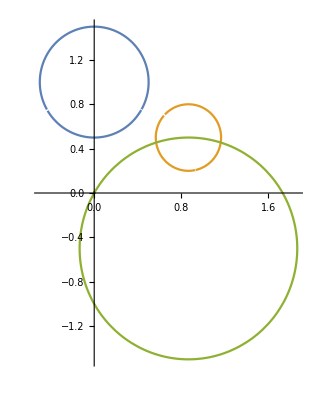

```mathematica
c1={10^-10,1};
c2={Cos[210°],Sin[210°]}
c3={Cos[330°],Sin[330°]}

a1=.5;
a2=.3;
a3=1;

x1=c1[[1]];
y1=c1[[2]];

x2=c2[[1]];
y2=c2[[2]];

x3=c3[[1]];
y3=c3[[2]];


PolarPlot[{
√(x1^2+y1^2)Cos[θ-ArcTan[y1/x1]]+√(a1^2-(x1^2+y1^2)*Sin[θ-ArcTan[y1/x1]]^2),
√(x2^2+y2^2)Cos[θ-ArcTan[y2/x2]]+√(a2^2-(x2^2+y2^2)*Sin[θ-ArcTan[y2/x2]]^2),
√(x3^2+y3^2)Cos[θ-ArcTan[y3/x3]]+√(a3^2-(x3^2+y3^2)*Sin[θ-ArcTan[y3/x3]]^2)},{θ,0,2π}];
```

```mathematica
Solve[{√(x2^2+y2^2)Cos[θ-ArcTan[y2/x2]]+√(a2^2-(x2^2+y2^2)*Sin[θ-ArcTan[y2/x2]]^2)==
√(x3^2+y3^2)Cos[θ-ArcTan[y3/x3]]+√(a3^2-(x3^2+y3^2)*Sin[θ-ArcTan[y3/x3]]^2)}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{θ→-2.35619-19.1059 ⅈ},{θ→-2.35619+19.1059 ⅈ},{θ→0.373031},{θ→2.35619-19.1059 ⅈ},{θ→2.35619+19.1059 ⅈ}}

```mathematica
Clear["Global`*"]
Expand[(x-x1)^2+(y-y1)^2==r1^2];
Expand[(x-y2)^2+(y+y2)^2==r2^2];


x^2-2 x x1+x1^2+y^2-2 y y1+y1^2==r1^2;
-x^2+2 x x1-x1^2-y^2+2 y y1-y1^2==-r1^2;
x^2+y^2-2 x y2+2 y y2+2 y2^2==(r2^2);
-x^2+2 x x1-x1^2-y^2+2 y y1-y1^2+x^2+y^2-2 x y2+2 y y2+2 y2^2==-r1^2+(r2^2);



Solve[2 x x1-x1^2+2 y y1-y1^2-2 x y2+2 y y2+2 y2^2==-r1^2+r2^2,x];


x->(-r1^2+r2^2+x1^2-2 y y1+y1^2-2 y y2-2 y2^2)/(2 (x1-y2));

Solve[x^2-2 x x1+x1^2+y^2-2 y y1+y1^2==r1^2/.x->(-r1^2+r2^2+x1^2-2 y y1+y1^2-2 y y2-2 y2^2)/(2 (x1-y2)),y];


c1={10^-10,1};
c2={Cos[210°],Sin[210°]};
c3={Cos[330°],Sin[330°]};

r1=.3;
r2=.3;
r3=1;

x1=c1[[1]];
y1=c1[[2]];

x2=c2[[1]];
y2=c2[[2]];

x3=c3[[1]];
y3=c3[[2]];
{{y->(2 y1-(r1^2 y1)/(x1-y2)^2+(r2^2 y1)/(x1-y2)^2+(x1^2 y1)/(x1-y2)^2+y1^3/(x1-y2)^2-(2 x1 y1)/(x1-y2)-(r1^2 y2)/(x1-y2)^2+(r2^2 y2)/(x1-y2)^2+(x1^2 y2)/(x1-y2)^2+(y1^2 y2)/(x1-y2)^2-(2 x1 y2)/(x1-y2)-(2 y1 y2^2)/(x1-y2)^2-(2 y2^3)/(x1-y2)^2-√((-2 y1+(r1^2 y1)/(x1-y2)^2-(r2^2 y1)/(x1-y2)^2-(x1^2 y1)/(x1-y2)^2-y1^3/(x1-y2)^2+(2 x1 y1)/(x1-y2)+(r1^2 y2)/(x1-y2)^2-(r2^2 y2)/(x1-y2)^2-(x1^2 y2)/(x1-y2)^2-(y1^2 y2)/(x1-y2)^2+(2 x1 y2)/(x1-y2)+(2 y1 y2^2)/(x1-y2)^2+(2 y2^3)/(x1-y2)^2)^2-4 (1+y1^2/(x1-y2)^2+(2 y1 y2)/(x1-y2)^2+y2^2/(x1-y2)^2) (-r1^2+x1^2+y1^2+r1^4/(4 (x1-y2)^2)-(r1^2 r2^2)/(2 (x1-y2)^2)+r2^4/(4 (x1-y2)^2)-(r1^2 x1^2)/(2 (x1-y2)^2)+(r2^2 x1^2)/(2 (x1-y2)^2)+x1^4/(4 (x1-y2)^2)-(r1^2 y1^2)/(2 (x1-y2)^2)+(r2^2 y1^2)/(2 (x1-y2)^2)+(x1^2 y1^2)/(2 (x1-y2)^2)+y1^4/(4 (x1-y2)^2)+(r1^2 x1)/(x1-y2)-(r2^2 x1)/(x1-y2)-x1^3/(x1-y2)-(x1 y1^2)/(x1-y2)+(r1^2 y2^2)/(x1-y2)^2-(r2^2 y2^2)/(x1-y2)^2-(x1^2 y2^2)/(x1-y2)^2-(y1^2 y2^2)/(x1-y2)^2+(2 x1 y2^2)/(x1-y2)+y2^4/(x1-y2)^2)))/(2 (1+y1^2/(x1-y2)^2+(2 y1 y2)/(x1-y2)^2+y2^2/(x1-y2)^2))},{y->(2 y1-(r1^2 y1)/(x1-y2)^2+(r2^2 y1)/(x1-y2)^2+(x1^2 y1)/(x1-y2)^2+y1^3/(x1-y2)^2-(2 x1 y1)/(x1-y2)-(r1^2 y2)/(x1-y2)^2+(r2^2 y2)/(x1-y2)^2+(x1^2 y2)/(x1-y2)^2+(y1^2 y2)/(x1-y2)^2-(2 x1 y2)/(x1-y2)-(2 y1 y2^2)/(x1-y2)^2-(2 y2^3)/(x1-y2)^2+√((-2 y1+(r1^2 y1)/(x1-y2)^2-(r2^2 y1)/(x1-y2)^2-(x1^2 y1)/(x1-y2)^2-y1^3/(x1-y2)^2+(2 x1 y1)/(x1-y2)+(r1^2 y2)/(x1-y2)^2-(r2^2 y2)/(x1-y2)^2-(x1^2 y2)/(x1-y2)^2-(y1^2 y2)/(x1-y2)^2+(2 x1 y2)/(x1-y2)+(2 y1 y2^2)/(x1-y2)^2+(2 y2^3)/(x1-y2)^2)^2-4 (1+y1^2/(x1-y2)^2+(2 y1 y2)/(x1-y2)^2+y2^2/(x1-y2)^2) (-r1^2+x1^2+y1^2+r1^4/(4 (x1-y2)^2)-(r1^2 r2^2)/(2 (x1-y2)^2)+r2^4/(4 (x1-y2)^2)-(r1^2 x1^2)/(2 (x1-y2)^2)+(r2^2 x1^2)/(2 (x1-y2)^2)+x1^4/(4 (x1-y2)^2)-(r1^2 y1^2)/(2 (x1-y2)^2)+(r2^2 y1^2)/(2 (x1-y2)^2)+(x1^2 y1^2)/(2 (x1-y2)^2)+y1^4/(4 (x1-y2)^2)+(r1^2 x1)/(x1-y2)-(r2^2 x1)/(x1-y2)-x1^3/(x1-y2)-(x1 y1^2)/(x1-y2)+(r1^2 y2^2)/(x1-y2)^2-(r2^2 y2^2)/(x1-y2)^2-(x1^2 y2^2)/(x1-y2)^2-(y1^2 y2^2)/(x1-y2)^2+(2 x1 y2^2)/(x1-y2)+y2^4/(x1-y2)^2)))/(2 (1+y1^2/(x1-y2)^2+(2 y1 y2)/(x1-y2)^2+y2^2/(x1-y2)^2))}}
```

{{y→0.75-0.132288 ⅈ},{y→0.75+0.132288 ⅈ}}